```mathematica
Remove[a]
```

```mathematica
a=Import["~/LR5-SSR_2025-11-26_H15_M54_S34/LR5-SSR_2025-11-28_H14_M21_S55.csv","CSV"];
```

```mathematica
a[[1]]
```

{2025 Nov 28 14:21:55.439,0.12,13.5625,4.1875,1}

```mathematica
a[[Length[a]]]
```

{2025 Nov 28 17:57:18.664,12923.3,-16.8125,-17.5625,1}

```mathematica
Dimensions[a]
```

{112175,5}

```mathematica
b=Table[{a[[i,2]]*10,a[[i,3]]},{i,1,Length[a],10}];
```

```mathematica
c=Table[{a[[i,2]]*10,a[[i,4]]},{i,1,Length[a],10}];
```

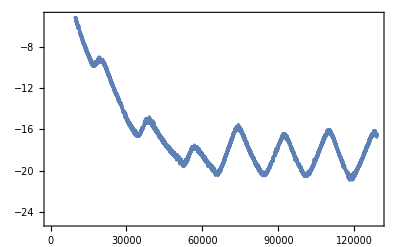

```mathematica
g1=ListPlot[b,Axes->False,Frame->True,PlotRange->{-25,-5},Joined->True]
```

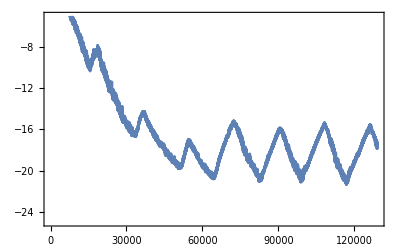

```mathematica
g2=ListPlot[c,Axes->False,Frame->True,PlotRange->{-25,-5},Joined->True]
```

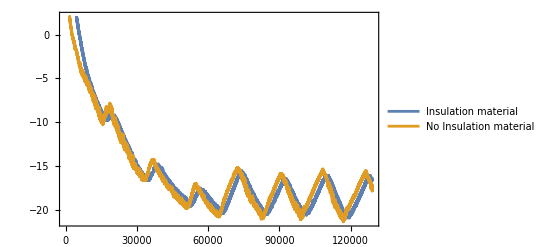

```mathematica
ListPlot[{b,c},PlotLegends->{"Insulation material","No Insulation material"},
Axes->False,Frame->True,Joined->True]
```

```mathematica
b1=Table[a[[i,3]],{i,1,Length[a],10}];
```

```mathematica
c1=Table[a[[i,4]],{i,1,Length[a],10}];
```

```mathematica
b1[[1]]
```

13.5625

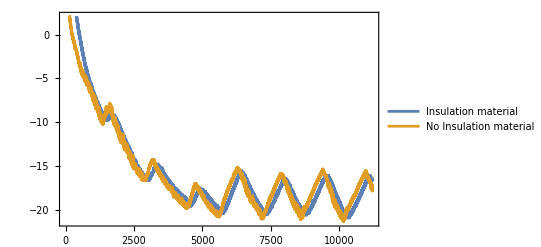

```mathematica
ListPlot[{b1,c1},PlotLegends->{"Insulation material","No Insulation material"},
Axes->False,Frame->True,Joined->True]
```

```mathematica
b2=Table[a[[i,3]],{i,90000,100000}];
```

```mathematica
c2=Table[a[[i,4]],{i,90000,100000}];
```

```mathematica
Max[c2]-Max[b2]
```

0.75

## CrossCorrelation

```mathematica
w1=Table[a[[i,3]],{i,50000,110000}];
```

```mathematica
w2=Table[a[[i,4]],{i,50000,110000}];
```

```mathematica
f1=Fourier[w1];
```

```mathematica
f2=Conjugate[Fourier[w2]];
```

```mathematica
ff=f1*f2;
```

```mathematica
c1=Re[InverseFourier[ff]]/(Norm[w1]Norm[w2]);
```

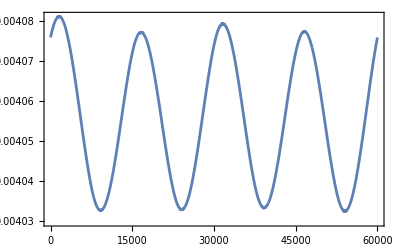

```mathematica
ListPlot[Re[c1],Joined->True,PlotRange->All,Axes->False,Frame->True]
```

```mathematica
mc=Max[c1]
```

0.00408124

```mathematica
z=0;
```

```mathematica
Do[If[c1[[i]]==mc,z=i],{i,Length[c1]}]
```

```mathematica
Print[z]
```

1590

```mathematica
a[[z,2]]
```

182.79